# , , row=8 , ,

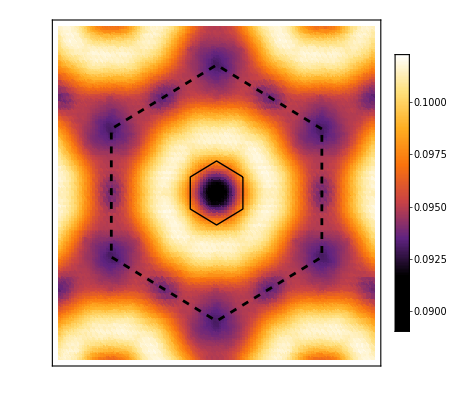

```mathematica
Needs["MaTeX`"]
d1=Import["ssf8a.dat","Table"];
n=40;aspRatio=1;padding=0.9;
colorF=(ColorData["SunsetColors"][Rescale[#,{0.2,1.}]]&);
plotRange={Full,Full,Full};
frameStyle=Directive[Black,FontSize->2,FontFamily->"Latin Modern Roman"];
gridL={{1,n+1,2 n+1,3 n+1,4 n+1,5 n+1},None};
gridLstyle=Directive[Black];
xTicks={{-3 π,MaTeX["-3\\pi",Magnification->0.90]},{0,MaTeX["0",Magnification->0.90]},{3 π-0.5,MaTeX["3\\pi ",Magnification->0.90]}};
yTicks={{-3 π,MaTeX["-3\\pi",Magnification->0.90]},{0,MaTeX["0",Magnification->0.90]},{3 π-0.3,MaTeX["3\\pi",Magnification->0.90]}};
gfbz=Graphics[{Black,Line[{{π/2,π/(2 Sqrt[3])},{0,π/Sqrt[3]},{-(π/2),π/(2 Sqrt[3])},{-(π/2),-(π/(2 Sqrt[3]))},{0,-(π/Sqrt[3])},{π/2,-(π/(2 Sqrt[3]))},{π/2,π/(2 Sqrt[3])}}]}];
gebz=Graphics[{Black,Dashed,Thickness[0.005],Line[{{2 π,(2 π)/Sqrt[3]},{0,(4 π)/Sqrt[3]},{-2 π,(2 π)/Sqrt[3]},{-2 π,-((2 π)/Sqrt[3])},{0,-((4 π)/Sqrt[3])},{2 π,-((2 π)/Sqrt[3])},{2 π,(2 π)/Sqrt[3]}}]}];
p1=Show[With[{l=d1},ListDensityPlot[l,Frame->True,FrameStyle->frameStyle,ColorFunction->colorF,ColorFunctionScaling->True,PlotRange->plotRange,FrameTicks->{{yTicks,None},{xTicks,None}},AspectRatio->aspRatio,PlotRangePadding->padding,InterpolationOrder->Automatic,PlotLegends->Automatic]],gfbz,gebz]
(*GraphicsGrid[{{p0,p1}},Spacings->{0,0}]*)
```